# Initialization

```mathematica
HaToeV=27.21138602;
```

```mathematica
SizeLegend=1.5;
```

```mathematica
SetDirectory["~/Dropbox/Manuscripts/CC4/Data"];
```

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,mathpazo,xcolor,bm,mhchem}"}];
```

# XLS

### Methods

```mathematica
Met={"CC2","CCSD","CCSDT-3","CC3","CCSDT","CC4","CCSDTQ","CCSDTQP"};
```

### Charts

```mathematica
SizeLabel=1.25;
SizeFrameLabel=2;
ChartCC3={
Frame->True,
BaseStyle->16,
BarSpacing->{0,0},
GridLines->{Automatic,All},
AspectRatio->4,
PlotTheme->"Scientific",
Joined->True,
ChartElementFunction->"Rectangle",
ImageSize->250,
BarOrigin->Left
};
```

```mathematica
BarChart[Ea⟦;;,2⟧,PlotLabel->MaTeX["\\text{Absorption energy}",Magnification->2],ChartStyle->LightBlue,
ChartCC3,PlotRange->{{-1.0,0.0},{1,Length[Ea]}},
FrameLabel->{None,MaTeX["\\text{MSE (eV)}",Magnification->SizeFrameLabel]},ChartLabels->Placed[Table[Rotate[MaTeX[StringJoin["\\text{",Ea⟦k,1⟧,"}"],Magnification->SizeLabel],0 Degree],{k,Length[Ea]}],Right]
]
Export["Figure-3a.pdf",%];
BarChart[Ef⟦;;,2⟧,PlotLabel->MaTeX["\\text{Fluorescence energy}",Magnification->2],ChartStyle->LightRed,
ChartCC3,PlotRange->{{-1.0,0.0},{1,Length[Ef]}},
FrameLabel->{None,MaTeX["\\text{MSE (eV)}",Magnification->SizeFrameLabel]},
ChartLabels->Placed[Table[Rotate[MaTeX[StringJoin["\\text{",Ef⟦k,1⟧,"}"],Magnification->SizeLabel],0 Degree],{k,Length[Ef]}],Right]
]
Export["Figure-3b.pdf",%];
BarChart[Ead⟦;;,2⟧,PlotLabel->MaTeX["\\text{Adiabatic energy}",Magnification->2],ChartStyle->LightGreen,
ChartCC3,PlotRange->{{-1.0,0.0},{1,Length[Ead]}},
FrameLabel->{None,MaTeX["\\text{MSE (eV)}",Magnification->SizeFrameLabel]},
ChartLabels->Placed[Table[Rotate[MaTeX[StringJoin["\\text{",Ead⟦k,1⟧,"}"],Magnification->SizeLabel],0 Degree],{k,Length[Ead]}],Right]
]
Export["Figure-3c.pdf",%];
```

### MSE/AVDZ

```mathematica
MSEDZ=Import["CC4-Bench.xlsx"]⟦1,4;;28,3;;10⟧;
MSEDZ=Table[MSEDZ⟦a,b⟧-MSEDZ⟦a,Length[Met]⟧,{a,Length[MSEDZ]},{b,Length[Met]-1}];
Table[SetAccuracy[Mean[MSEDZ⟦;;,a⟧],4],{a,Length[Met]-1}]
Table[SetAccuracy[Mean[Abs[MSEDZ⟦;;,a⟧]],4],{a,Length[Met]-1}]
Table[SetAccuracy[Max[Abs[MSEDZ⟦;;,a⟧]],4],{a,Length[Met]-1}]
```

{0.02,0.075,0.03,0.013,0.0008,-0.0004,0.0004}

{0.257,0.109,0.04,0.028,0.018,0.003,0.002}

{0.575,0.324,0.196,0.152,0.047,0.011,0.007}

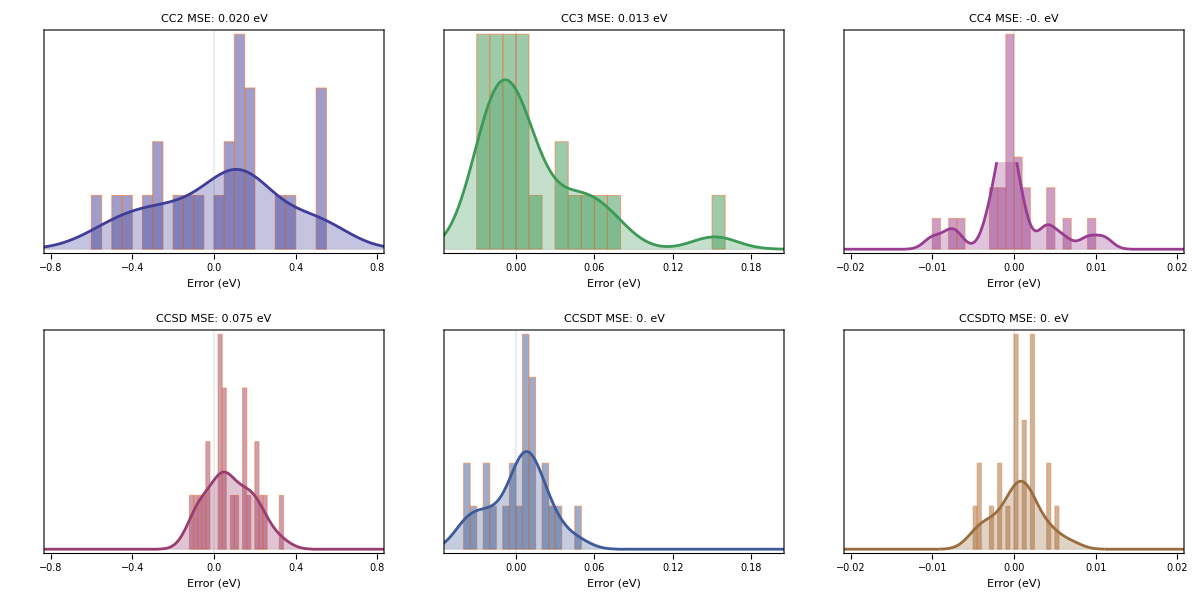

```mathematica
MSEDZ=Import["CC4-Bench.xlsx"]⟦1,4;;28,3;;10⟧;
MSEDZ=Table[MSEDZ⟦a,b⟧-MSEDZ⟦a,Length[Met]⟧,{a,Length[MSEDZ]},{b,Length[Met]-1}];
graph=Table[
Show[{
Histogram[MSEDZ⟦2;;,m⟧,20,"PDF",PlotTheme->"Scientific",BaseStyle->14,PlotRange->{{-0.1,0.1},Automatic},FrameLabel->{"Error (eV)",None},ChartStyle->{Directive[Opacity[0.5],ColorData[1,"ColorList"]⟦m⟧]},FrameTicks->{Automatic,None},PlotLabel->Style[Met⟦m⟧<>" MSE: "<>ToString[SetAccuracy[Mean[MSEDZ⟦;;,m⟧],4]]<>" eV",14]]
,
SmoothHistogram[DeleteCases[MSEDZ⟦2;;,m⟧,""],Automatic,"PDF",PlotRange->{{-1,1},Automatic},PlotStyle->Directive[ColorData[1,"ColorList"]⟦m⟧,Thickness[0.01]],Filling->Bottom,PlotTheme->"Web"]
},ImageSize->200]
,{m,Length[Met]-1}];
Grid[
{{Show[graph⟦1⟧,PlotRange->{{-0.8,0.8},All}],
Show[graph⟦4⟧,PlotRange->{{-0.05,0.2},All}],
Show[graph⟦6⟧,PlotRange->{{-0.02,0.02},All}]
}
,
{
Show[graph⟦2⟧,PlotRange->{{-0.8,0.8},All}],
Show[graph⟦5⟧,PlotRange->{{-0.05,0.2},All}],
Show[graph⟦7⟧,PlotRange->{{-0.02,0.02},All}]
}}
]
Export["histograms_MSE_AVDZ.pdf",%];
```

### MAE/AVDZ

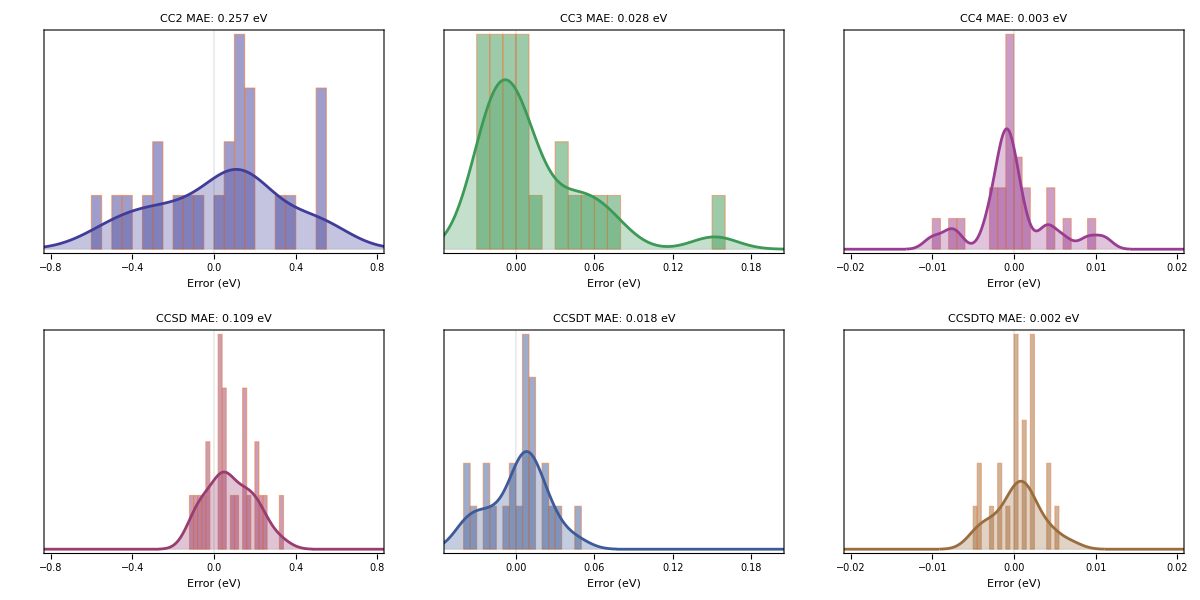

```mathematica
MAEDZ=Import["CC4-Bench.xlsx"]⟦1,4;;28,3;;10⟧;
MAEDZ=Table[MAEDZ⟦a,b⟧-MAEDZ⟦a,Length[Met]⟧,{a,Length[MAEDZ]},{b,Length[Met]-1}];
graph=Table[
Show[{
Histogram[MAEDZ⟦2;;,m⟧,20,"PDF",PlotTheme->"Scientific",BaseStyle->14,PlotRange->{{-0.25,0.25},All},FrameLabel->{"Error (eV)",None},ChartStyle->{Directive[Opacity[0.5],ColorData[1,"ColorList"]⟦m⟧]},FrameTicks->{Automatic,None},PlotLabel->Style[Met⟦m⟧<>" MAE: "<>ToString[SetAccuracy[Mean[Abs[MAEDZ⟦;;,m⟧]],4]]<>" eV",14]]
,
SmoothHistogram[DeleteCases[MAEDZ⟦2;;,m⟧,""],Automatic,"PDF",PlotRange->{{-1,1},All},PlotStyle->Directive[ColorData[1,"ColorList"]⟦m⟧,Thickness[0.01]],Filling->Bottom,PlotTheme->"Web"]
},ImageSize->200]
,{m,Length[Met]-1}];
Grid[
{{Show[graph⟦1⟧,PlotRange->{{-0.8,0.8},All}],
Show[graph⟦4⟧,PlotRange->{{-0.05,0.2},All}],
Show[graph⟦6⟧,PlotRange->{{-0.02,0.02},All}]
}
,
{
Show[graph⟦2⟧,PlotRange->{{-0.8,0.8},All}],
Show[graph⟦5⟧,PlotRange->{{-0.05,0.2},All}],
Show[graph⟦7⟧,PlotRange->{{-0.02,0.02},All}]
}}
]
Export["histograms_MAE_AVDZ.pdf",%];
```

# Composite method

```mathematica
Met={"CC2","CCSD","CC3","CCSDT","CC4","CCSDTQ","CCSDTQP"};
ΔE=Import["CC4-Bench.xlsx"]⟦1,4;;28,{3,4,6,7,8,9,10}⟧;
Ref=ΔE⟦;;,Length[Met]⟧;
ΔΔE=Table[ΔE⟦a,b⟧-Ref⟦a⟧,{a,Length[ΔE]},{b,Length[Met]-1}];
```

```mathematica
Table[{Met⟦b⟧,1/Length[ΔE]∑_(a=1)^Length[ΔE] Abs[ΔE⟦a,b⟧-Ref⟦a⟧]},{b,Length[Met]}]//TableForm
```

CC2 | 0.25652
CCSD | 0.1088
CC3 | 0.02796
CCSDT | 0.01768
CC4 | 0.00324
CCSDTQ | 0.00224
CCSDTQP | 0.

```mathematica
Table[{nMet,Minimize[1/(Length[ΔE]nMet)∑_(a=1)^Length[ΔE] Abs[∑_(b=1)^nMet Subscript[c, b] ΔE⟦a,b⟧-Ref⟦a⟧],Table[Subscript[c, b],{b,nMet}]]},{nMet,1,Length[Met]}]//TableForm
```

1 | 0.235771
c_1→0.989508
2 | 0.0336438 | 
c_1→-0.333655 | c_2→1.32719
3 | 0.00704452 |  | 
c_1→-0.0945742 | c_2→0.177027 | c_3→0.916487
4 | 0.00147788 |  |  | 
c_1→-0.0244118 | c_2→-0.168344 | c_3→-0.161263 | c_4→1.35553
5 | 0.00023653 |  |  |  | 
c_1→-0.00844998 | c_2→-0.0624675 | c_3→-0.00812754 | c_4→0.343232 | c_5→0.736281
6 | 0.000103759 |  |  |  |  | 
c_1→-0.000546859 | c_2→-0.0273444 | c_3→0.0202355 | c_4→-0.0037354 | c_5→0.13115 | c_6→0.880425
7 | 1.64619×10^-12 |  |  |  |  |  | 
c_1→2.34336×10^-11 | c_2→-3.13962×10^-10 | c_3→4.15701×10^-10 | c_4→-1.22928×10^-9 | c_5→-5.75167×10^-10 | c_6→1.81275×10^-8 | c_7→1.